## ATLAS Signal region and Constraints from LHC

```mathematica
SetDirectory[NotebookDirectory[]];
ProjectDirectory="/Users/yoshi/Dropbox/Study_D/projects/z2j/";
```

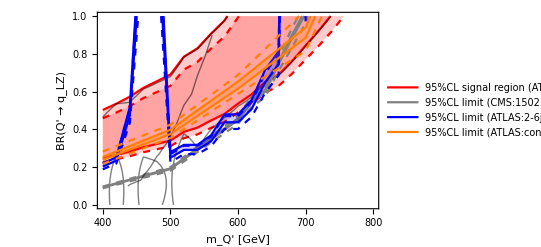

ATLAS Signal region and constraints from other LHC analyses in the BR(Q' ¥rightarrow q_L Z) vs. VLQ mass plane. The red region shows the 95%CL ATLAS signal region, while gray- and blue-shaded regions are 95%CL constraint from the CMS on-Z SUSY search and ATLAS 2-6 jet +E_T^{¥rm miss} searches, respectively.

```mathematica
(* signal region from ATLAS 2lepton +2>=jets +MET *)
(* BR(bp > d z) = 1 case *)
LOlist={{200,92,29.6},{300,91.387,29.6},{400,67.099,29.6},{500,36.228,29.6},{600,14.674,29.6},{620,12.112,29.6},{640,10.038,29},{660,8.209,29.6},{680,6.773,29.6},{700,5.583,29.6},{720,4.598,29.6},{740,3.785,29.6},{760,3.132,29.6}};
NLOlist={{400,110.222,29.6},{500,58.374,29.6},{600,23.162,29.6},{700,9.567,29.6},{800,3.708,29.6}};
NNLOlist={{400,117,6,29.6},{420,103,5,29.6},{440,90,5,29.6},{460,77,4,29.6},{480,69,4,29.6},{500,62,3,29.6},{520,48,3,29.6},{540,43,2,29.6},{560,36,2,29.6},{580,31,2,29.6},{600,25,1,29.6},{620,21,1,29.6},{640,17,1,29.6},{660,15.1,0.9,29.6},{680,12.4,0.8,29.6},{700,10.1,0.6,29.6},{720,8.4,0.5,29.6},{740,7,0.4,29.6},{760,5.8,0.4,29.6},{780,4.8,0.3,29.6},{800,4.1,0.3,29.6}};
limit=NNLOlist;
limitz=NNLOlist;
(* BR(bp > u w-) = 1 case *)
NNLOlist={{400,15,9,29.6},{420,0.001,4,29.6},{440,14,6,29.6},{460,4,3,29.6},{480,6,3,29.6},{500,9,3,29.6},{520,1,1,29.6},{540,7,2,29.6},{560,4,1,29.6},{580,1.9,0.9,29.6},{600,1.5,0.7,29.6},{620,1.8,0.7,29.6},{640,0.9,0.5,29.6},{660,1,0.4,29.6},{680,0.8,0.3,29.6},{700,0.6,0.3,29.6},{720,0.4,0.2,29.6},{740,0.4,0.2,29.6},{760,0.6,0.2,29.6},{780,0.4,0.1,29.6},{800,0.5,0.2,29.6}};
limitw=NNLOlist;

SignalUpperLimit=Flatten[Table[{limitz[[i,1]],j,(j^2 limitz[[i,2]]+(1-j)^2 limitw[[i,2]])/(18.4+11.2)},{j,0,1,0.01},{i,20}],1];
SignalLowerLimit=Flatten[Table[{limitz[[i,1]],j,(j^2 limitz[[i,2]]+(1-j)^2 limitw[[i,2]])/(18.4-11.2)},{j,0,1,0.01},{i,20}],1];
ContourSignalUpper=ListContourPlot[SignalUpperLimit,Contours->{1},ContourShading->None];
ContourSignalLower=ListContourPlot[SignalLowerLimit,Contours->{1},ContourShading->None];

(*limitmean=Table[{list[[i,1]],(18.4/list[[i,2]])^0.25 0.1},{i,1,Length[list]}];
limitupper=Table[{list[[i,1]],(29.6/list[[i,2]])^0.25 0.1},{i,1,Length[list]}];
limitlower=Table[{list[[i,1]],(7.2/list[[i,2]])^0.25 0.1},{i,1,Length[list]}];*)
limitupper1=Table[{limit[[i,1]],Sqrt[(18.4+11.2)/limit[[i,2]]]},{i,1,Length[limit]}];
limitlower1=Table[{limit[[i,1]],Sqrt[(18.4-11.2)/limit[[i,2]]]},{i,1,Length[limit]}];
limitupper2=Table[{limit[[i,1]],Sqrt[(18.4+11.2)/(limit[[i,2]]1.2)]},{i,1,Length[limit]}];
limitlower2=Table[{limit[[i,1]],Sqrt[(18.4-11.2)/(limit[[i,2]]1.2)]},{i,1,Length[limit]}];
plimit=ListPlot[{limitupper1,limitlower1,limitupper2,limitlower2},Joined->True,PlotStyle->{Red,Red,{Red,Dashed},{Red,Dashed}},Frame->True,FrameLabel->{Text@Style["m_Q' [GeV]",17],Text@Style["BR(Q' → q_LZ)",15]},PlotLegends->Placed[{"95%CL signal region (ATLAS:1503.03290)"},After],Filling->{1->{2},3->{4}},PlotRange->{{100,1000},{0,1}}];
(*Show[plimit,Graphics[Text[Style["BR(B->bZ) = 1",13],Scaled[{0.85,0.9}]]],
ImageSize->400]*)

(* limit from ATLAS 2-6jet + MET 1405.7875 *)
(* BR(bp > d z) = 1 case *)
LOlimit={{400,815.915,270},{500,87.65,35},{600,45.093,35},{700,18.821,35}};
NLOlimit={{400,1173,270},{500,126,35},{600,72,35},{700,30,35}};
NNLOlimit={{400,1330,100,270},{420,1150,80,270},{440,570,50,270},{460,180,20,270},{480,180,20,270},{500,140,15,35},{520,120,10,35},{540,120,10,35},{560,104,9,35},{580,80,7,35},{600,80,7,35},{620,69,6,35},{640,54,5,35},{660,47,4,35},{680,8,1,35},{700,33,3,35}};
limitz=NNLOlimit;
limit=NNLOlimit;
(* BR(bp > u w-) = 1 case *)
NNLOlimit={{400,290,40,270},{420,63,16,39},{440,47,40,270},{460,290,40,270},{480,290,40,270},{500,46,8,35},{600,24,3,35},{700,24,3,35}};
limitw=NNLOlimit;

(* BR(bp > u w-)≠0 & BR(bp > u w-)≠0 case *)
NNLOlimit={{400,290,40,270},{420,63,16,39},{440,47,40,270},{460,290,40,270},{480,290,40,270},{500,46,8,35},{600,24,3,35},{700,24,3,35}};
limitw=NNLOlimit;


analysis="atlas_1405_7875";
LimitTable={};
rexpmax=-1;
S95max=-1;
imax=0;
Do[
brw=1-brz;
cmm=ToString[mm];
zzdata=Import[ProjectDirectory<>"analysis/results_local/"<>analysis<>"_"<>cmm<>"_z/evaluation/"<>analysis<>"_r_limits.txt","Table"];
zzdata=Drop[zzdata,2];
zwdata=Import[ProjectDirectory<>"analysis/results_local/"<>analysis<>"_"<>cmm<>"_zw/evaluation/"<>analysis<>"_r_limits.txt","Table"];
zwdata=Drop[zwdata,2];
wwdata=Import[ProjectDirectory<>"analysis/results_local/"<>analysis<>"_"<>cmm<>"_w/evaluation/"<>analysis<>"_r_limits.txt","Table"];
wwdata=Drop[wwdata,2];
Do[
Szz=zzdata[[i,2]];
dSzz=zzdata[[i,5]];
Sexp95=zzdata[[i,7]];
Sobs95=zzdata[[i,6]];
Szw=zwdata[[i,2]];
dSzw=zwdata[[i,5]];
Sww=wwdata[[i,2]];
dSww=wwdata[[i,5]];
rexp=(brz^2 Szz+2(brz Szz/2 +brw Sww/2)+brw^2 Sww-1.96Sqrt[brz^4 dSzz^2+4(brz brw/0.25)^2 dSzw^2+brw^4 dSww^2])/Sexp95;
If[rexp>rexpmax,rexpmax=rexp;imax=i;Sobs95max=Sobs95]
,{i,1,Length[zzdata]}];

AppendTo[LimitTable,{mm,brz,(brz^2 zzdata[[imax,2]]+2brz brw/0.25 zwdata[[imax,2]]+brw^2 wwdata[[imax,2]])/Sobs95max}],
{mm,400,700,20},{brz,0.1,0.9,0.2}]

(*LimitTable=Flatten[Table[{mm,j,(j^2 limitz[[i,2]]+0(1-j)^2 limitw[[i,2]])/limitz[[i,4]]},{j,0,1,0.1},{i,4}],1];
Contourlimit2=ListContourPlot[LimitTable,Contours->{1},ContourShading->None];
LimitTable=Flatten[Table[{limitz[[i,1]],j,(j^2 limitz[[i,2]]+0(1-j)^2 limitw[[i,2]])/limitz[[i,4]]},{j,0,1,0.1},{i,4}],1];*)
ContourLimit2=ListContourPlot[LimitTable,Contours->{1},ContourShading->None];

limit2=Table[{limit[[i,1]],limit[[i,4]]/limit[[i,2]]},{i,1,Length[limit]}];
limit2p=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]+limit[[i,3]])},{i,1,Length[limit]}];
limit2m=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]-limit[[i,3]])},{i,1,Length[limit]}];
AnalysisUnc=-0.07;
limitdiff=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]](1+AnalysisUnc))},{i,1,Length[limit]}];
plimit2=ListPlot[{limit2,limitdiff,limit2p,limit2m},Joined->True,PlotStyle->{Blue,{Blue,Dashed},{Blue,Dashed}},Frame->True,FrameLabel->{Text@Style["m_Q' [GeV]",17],Text@Style["BR(Q' → q_LZ)",15]},PlotLegends->Placed[{"95%CL limit (ATLAS:2-6jet+MET)"},After],Filling->{1->{2}},PlotRange->{{100,1000},{0,1}}];

(* limit from ATLAS Stop seach with 2 leptons 1403.4853 *)
(*limit={{100,0.1,3.1},{200,57.74,74},{300,8.221,3.1},{400,1.851,5.6},{500,0.757,3.1},{600,0.175,3.1},{700,0.105,3.1}};*)
LOlimit={{400,2.158,5.6},{500,0.076,3.1},{600,0.218,3.1},{700,0.161,3.1}};
limit=LOlimit;
limit2=Table[{limit[[i,1]],limit[[i,3]]/limit[[i,2]]},{i,1,Length[limit]}];
plimit3=ListPlot[limit2,Joined->True,PlotStyle->{Darker[Green]},Frame->True,FrameLabel->{Text@Style["m_Q' [GeV]",17],Text@Style["BR(Q' → q_LZ)",15]},PlotLegends->Placed[{"95%CL limit (ATLAS:Stop search)"},After],Filling->Top,PlotRange->{{100,1000},{0,1}}];

(* limit from atlas_conf_2013_047 *)
(*limit={{100,0.1,3.1},{200,215.656,92.4},{300,170.303,92.4},{400,181.89,81.2},{500,129.522,81.2},{600,70.605,81.2},{700,8.34,15.5}};*)
LOlimit={{400,205.512,81.2},{500,128.453,81.2},{600,75.878,81.2},{700,9.166,15.5}};
NLOlimit={{400,302.291,81.2},{500,189.586,81.2},{600,116.51,81.2},{700,14.67,15.5}};
NNLOlimit={{400,330,43,81.2},{500,210,19,81.2},{600,128,10,81.2},{700,17,2,15.5},{800,8.9,0.9,15.5}};
limit=NNLOlimit;
limit2=Table[{limit[[i,1]],limit[[i,4]]/limit[[i,2]]},{i,1,Length[limit]}];
limit2p=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]+limit[[i,3]])},{i,1,Length[limit]}];
limit2m=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]-limit[[i,3]])},{i,1,Length[limit]}];
limitdiffp=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]1.03)},{i,1,Length[limit]}];
limitdiffm=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]0.97)},{i,1,Length[limit]}];
plimit4=ListPlot[{limitdiffp,limitdiffm,limit2p,limit2m},Joined->True,PlotStyle->{Orange,Orange,{Orange,Dashed},{Orange,Dashed}},Frame->True,FrameLabel->{Text@Style["m_Q' [GeV]",17],Text@Style["BR(Q' → q_LZ)",15]},PlotLegends->Placed[{"95%CL limit (ATLAS:conf_2013_047)"},After],Filling->{1->{2}},PlotRange->{{100,1000},{0,1}}];

(* limit from cms_1502.06031 *)
LOlimit={{100,6061.035,107},{200,896.668,20},{300,369.237,20},{400,63.383,7.6},{500,28.518,7.6},{600,11.312,7.6},{620,9.091,7.6},{640,7.628,7.6},{660,6.39,7.6},{680,5.329,7.6},{700,4.511,7.6},{720,3.708,7.6},{740,3.083,7.6},{760,2.594,7.6}};
(*limit={{100,6061.035,107},{200,896.668,20},{300,369.237,20},{400,63.383,7.6},{500,28.518,7.6},{600,11.312,7.6},{700,4.511,7.6},{720,7.6},{740,7.6},{760,7.6}};*)
NLOlimit={{400,86.925,7.6},{500,38.04,7.6},{600,16.709,7.6},{700,7.381,7.6},{800,3.061,7.6}};
NNLOlimit={{400,82.1,4,7.6},{500,40,2,7.6},{600,16.9,0.8,7.6},{620,14.0,0.7,7.6},{640,12.7,0.6,7.6},{660,10.2,0.5,7.6},{680,8.6,0.5,7.6},{700,7.5,0.4,7.6},{800,3.1,0.2,7.6}};
limit=NNLOlimit;
limit2=Table[{limit[[i,1]],limit[[i,4]]/limit[[i,2]]},{i,1,Length[limit]}];
limit2p=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]+limit[[i,3]])},{i,1,Length[limit]}];
limit2m=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]-limit[[i,3]])},{i,1,Length[limit]}];
limit2diff=Table[{limit[[i,1]],limit[[i,4]]/(limit[[i,2]]0.98)},{i,1,Length[limit]}];
plimit5=ListPlot[{limit2,limit2diff,limit2p,limit2m},Joined->True,PlotStyle->{Gray,Gray,{Gray,Dashed},{Gray,Dashed}},Frame->True,FrameLabel->{Text@Style["m_Q' [GeV]",17],Text@Style["BR(Q' → q_LZ)",15]},PlotLegends->Placed[{"95%CL limit (CMS:1502.06031)"},After],Filling->{1->{2}},PlotRange->{{100,1000},{0,1}}];

plotall=Show[{plimit,ContourSignalUpper,ContourSignalLower,plimit5,plimit2,ContourLimit2,plimit4},ImageSize->400,PlotRange->{{400,800},{0,1}}]
Export[ProjectDirectory<>"draft/figures/limit.pdf",plotall];
<<"!/opt/local/bin/pdf2ps /Users/yoshi/Dropbox/Study_D/projects/z2j/draft/figures/limit.pdf /Users/yoshi/Dropbox/Study_D/projects/z2j/draft/figures/limit.eps"
<<"!rm -rf /Users/yoshi/Dropbox/Study_D/projects/z2j/draft/figures/limit.pdf"
Print[ "ATLAS Signal region and constraints from other LHC analyses in the BR(Q' ¥rightarrow q_L Z) vs. VLQ mass plane. The red region shows the 95%CL ATLAS signal region, while gray- and blue-shaded regions are 95%CL constraint from the CMS on-Z SUSY search and ATLAS 2-6 jet +E_T^{¥rm miss} searches, respectively."]
```